```mathematica
Clear["Global`*"]
```

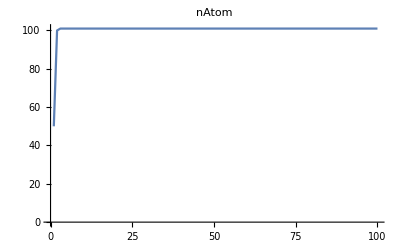

```mathematica
(*When doing one run*)
name ="test";
intensityy=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtomm=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionn=Flatten[Import[NotebookDirectory[]<>name<>"/inversion.dat"]];
ListLinePlot[nAtomm,PlotRange->All,PlotLabel->nAtom]
ListLinePlot[intensityy,PlotRange->All,PlotLabel->intensity]
ListLinePlot[inversionn,PlotRange->All,PlotLabel->inversion]
```

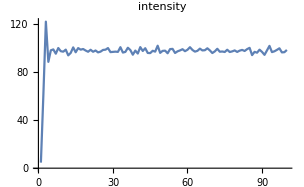
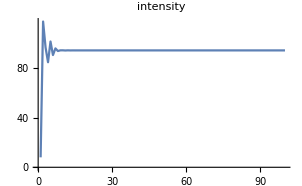

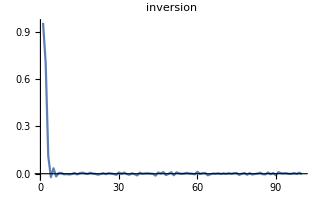
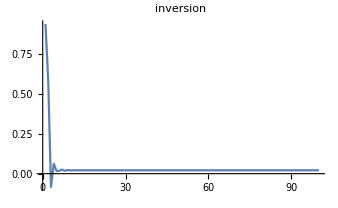

```mathematica
intensityy;
```